# Solving the Schrödinger Equation for Finite Potentials: From Atoms to Molecules and Solids

Noguera, V.*; Maisincho, B.; Morales, D .; Palma, A.* &  Salazar, A.* 
*School of Physical Sciences and Nanotechnology
School of Chemical Sciences and Engineering
Yachay Tech University, Urcuqui-Ecuador

## The finite potential well

The symbols we will use:
for energy (ℰ) -> EscscEEsc
(φ) -> EscjEsc
(ℏ) -> EschbEsc

```mathematica
eq = -ℏ^2/(2 m)φ''[x]==ℰ φ[x]
```

-(ℏ^2 φ''[x])/(2 m)==ℰ φ[x]

```mathematica
DSolve[eq, φ[x], x]
```

{{φ[x]→C[1] Cos[(√2 √m x √ℰ)/ℏ]+C[2] Sin[(√2 √m x √ℰ)/ℏ]}}

Solving with the corresponding boundary conditions: we see that c1=0 since φ[0]=C1=0

```mathematica
Solve[(√2 √m a √ℰ)/ℏ==n π, ℰ]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ℰ→(n^2 π^2 ℏ^2)/(2 a^2 m)}}

```mathematica
Sin[(√2 √m x √ℰ)/ℏ]/.{ℰ->(n^2 π^2 ℏ^2)/(2 m a^2)}//PowerExpand
```

Sin[(n π x)/a]

How  to  get  C?

```mathematica
Integrate[(C Sin[(n π x)/a])^2, {x, 0,a}]
```

1/4 a C^2 (2-Sin[2 n π]/(n π))

```mathematica
Solve[1/4 a C^2 (2-Sin[2 n π]/(n π))==1, C]
```

{{C→-2/(√(2 a-(a Sin[2 n π])/(n π)))},{C→2/(√(2 a-(a Sin[2 n π])/(n π)))}}

But notice that Sin[2nπ]=0

```mathematica
Solve[1/4 a C^2 (2-0/(n π))==1, C]
```

{{C→-(√2)/(√a)},{C→(√2)/(√a)}}

Let' s  define  the  wavefunction  φ  using  the  Piecewise  function : EscpwEsc

```mathematica
v[x_]:=Piecewise[{{50, x<0}, {0, 0<=x<=a}, {50, x>a}}]
```

```mathematica
φ[x_, n_]:=Piecewise[{{0, x<0}, {(√2)/(√a)Sin[(n π x)/a], 0<=x<=a}, {0, x>a}}]
```

```mathematica
Manipulate[
Plot[
2{ φ[x,n]+(n^2 π^2 ℏ^2)/(2 a^2 m), φ[x,n]^2+(n^2 π^2 ℏ^2)/(2 a^2 m),v[x],(n^2 π^2 ℏ^2)/(2 a^2 m)}/.{ℏ->1, m->1, n->nval, a ->aval}//Evaluate,{x,-0.1,aval+0.1},
PlotRange->{{-0.1,3.1},{-0.1,50}},
Filling->{2->{4}},
PlotStyle->{Blue,Green,{Red,Thickness[0.01]},Black},
ImageSize->300,
AspectRatio->1,
Ticks->{Automatic,None},
Exclusions->None],
{{aval,1.5},1,3},{{nval,1},1,5,1}, ControlPlacement->Right
]
```

It is observed when the value of a (length of the box) decreases the energy tends to increase. First of all it was found above that the expression of the energy is inversely proportional to the length a (E=(n^2 π^2 ℏ^2)/(2 a^2 m)). However, the fundamental reason is related with the uncertainty principle (ΔxΔp ≥ ℏ/2). Since we decrease the length a, the uncertainty position decreases. Therefore the momentum uncertainty should increase as well as the energy   (E=p^2/(2m)).

## Single finite potential well: model of a single atom

Let’s define the potential

```mathematica
v[x_]:=Piecewise[{{v0, x<-a/2}, {0, -a/2<=x<=a/2}, {v0, x>a/2}}]
```

```mathematica
la =2 (*bohr*);
vpot = 6.5 (*Subscript[E, h]*);
```

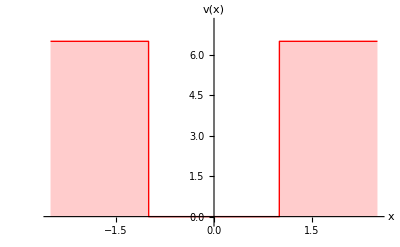

```mathematica
Plot[v[x]/.{v0->vpot,a->la},{x,-la-.5,la+.5},
AxesLabel->{"x","v(x)"},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,7.2}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis]
```

#### Solving the Schrödinger equation in a.u.

```mathematica
eq1=-1/2 ϕ1''[x]+v0 ϕ1[x]==ℰ ϕ1[x]
```

v0 ϕ1[x]-ϕ1''[x]/2==ℰ ϕ1[x]

```mathematica
DSolve[eq1, ϕ1[x], x]
```

{{ϕ1[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]+ⅇ^(-√2 x √(v0-ℰ)) C[2]}}

```mathematica
eq2=-1/2 ϕ2''[x]+0 ϕ2[x]==ℰ ϕ2[x]
```

-1/2 ϕ2''[x]==ℰ ϕ2[x]

```mathematica
DSolve[eq2, ϕ2[x],x]
```

{{ϕ2[x]→C[1] Cos[√2 x √ℰ]+C[2] Sin[√2 x √ℰ]}}

```mathematica
eq3=-1/2 ϕ3''[x]+v0 ϕ3[x]==ℰ ϕ3[x]
```

v0 ϕ3[x]-ϕ3''[x]/2==ℰ ϕ3[x]

```mathematica
DSolve[eq3, ϕ3[x], x]
```

{{ϕ3[x]→ⅇ^(√2 x √(v0-ℰ)) C[1]+ⅇ^(-√2 x √(v0-ℰ)) C[2]}}

Let’s define α = √(2(v0-ℰ))and β=√(2ℰ)

```mathematica
Do[Subscript[c,i]=.,{i,4}];
Do[Subscript[ϕ,i]=.,{i,4}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction φ:

```mathematica
φ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-a/2}, {Subscript[ϕ, 2][x], -a/2<=x<=a/2}, {Subscript[ϕ, 3][x], x>a/2}}]
```

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-a/2)==0;
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-a/2)==0;
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->a/2)==0;
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->a/2)==0;
```

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,4}], 
Table[Subscript[c, i], {i,4}]][[2]]//Normal
```

{{ⅇ^(-(a α)/2),-Cos[(a β)/2],Sin[(a β)/2],0},{ⅇ^(-(a α)/2) α,-β Sin[(a β)/2],-β Cos[(a β)/2],0},{0,Cos[(a β)/2],Sin[(a β)/2],-ⅇ^(-(a α)/2)},{0,-β Sin[(a β)/2],β Cos[(a β)/2],ⅇ^(-(a α)/2) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^(-(a α)/2) | -Cos[(a β)/2] | Sin[(a β)/2] | 0
ⅇ^(-(a α)/2) α | -β Sin[(a β)/2] | -β Cos[(a β)/2] | 0
0 | Cos[(a β)/2] | Sin[(a β)/2] | -ⅇ^(-(a α)/2)
0 | -β Sin[(a β)/2] | β Cos[(a β)/2] | ⅇ^(-(a α)/2) α)

```mathematica
mat2 = mat /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la}//FullSimplify
```

{{ⅇ^(-1.41421 √(6.5-ℰ)),-Cos[√2 √ℰ],Sin[√2 √ℰ],0},{1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[√2 √ℰ],-√2 √ℰ Cos[√2 √ℰ],0},{0,Cos[√2 √ℰ],Sin[√2 √ℰ],-ⅇ^(-1.41421 √(6.5-ℰ))},{0,-√2 √ℰ Sin[√2 √ℰ],√2 √ℰ Cos[√2 √ℰ],1.41421 ⅇ^(-1.41421 √(6.5-ℰ)) √(6.5-ℰ)}}

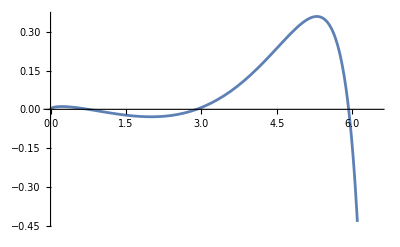

```mathematica
Plot[Det[mat2], {ℰ, 0, vpot}]
```

Here we found the energy levels. Notice that the values of ℰ where the function is cero satisfy the system of equations (mat*[coeff]=0).

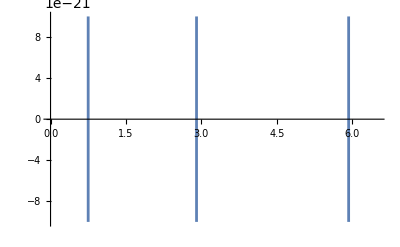

```mathematica
fig= Plot[Det[mat2], {ℰ, 0, vpot}, PlotRange->{-10^-20, 10^-20}]
```

```mathematica
fig[[1]]
```

{{{{},{},{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[2]],Line[{{0.748476,1.×10^-20},{0.748476,-1.×10^-20}}],Line[{{2.9027,-1.×10^-20},{2.9027,1.×10^-20}}],Line[{{5.92702,1.×10^-20},{5.92702,-1.×10^-20}}]}}},{}}

```mathematica
aproxroot = fig[[1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&, #]&//Sort
```

{0.748476,2.9027,5.92702}

```mathematica
rval=aproxroot//Map[FindRoot[Det[mat2], {ℰ, #}]&, #]&//Map[ℰ/.#&, #]&
```

{0.7495,2.9032,5.92714}

### Level 1

```mathematica
nval=1;
Do[Subscript[c,i]=., {i,4}];
Evaluate[Table[Subscript[c, i],{i,4}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.705376,0.0699299,0,0.705376}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

0.00633217

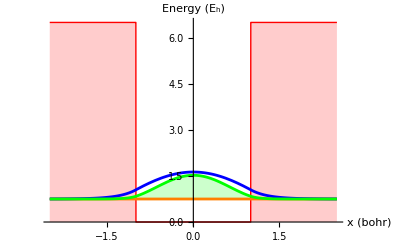

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x,-la-0.5, la+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

Upgrade until here, there is are some parts that are missing.

What is the probability of finding one electron within -a/2 ≤x≤a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x, -la/2, la/2}]
```

0.973742

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x, la/2, ∞}]
```

0.0131291

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.9999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 1.04083×10^-17 and 3.83571×10^-14 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

0.228641

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

## Two finite potential well: model of a single atom

Let’s define the potential

```mathematica
v[x_]:=Piecewise[{{v0, x<-a-b/2}, {0, -a-b/2<=x<=-b/2}, {v0, -b/2<x<b/2}, {0, b/2<x<a+b/2}, {v0, a+b/2<x}}]
```

```mathematica
la =2 (*bohr*);
lb=1 (*bohr*);
vpot = 6.5 (*Subscript[E, h]*);
```

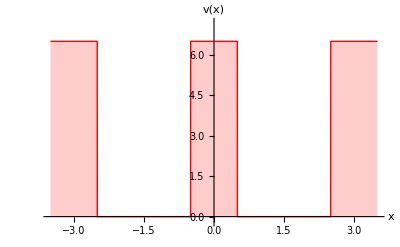

```mathematica
Plot[v[x]/.{v0->vpot,a->la,b->lb},{x,-la-lb-.5,la+lb+.5},
AxesLabel->{"x","v(x)"},
PlotStyle->{Red,Thick},
PlotRange->{Automatic,{-0.2,7.2}},
AxesStyle->Arrowheads[{0.0,0.03}],
Filling->Axis]
```

#### Solving the Schrödinger equation in a.u.

Let’s define α = √(2(v0-ℰ))and β=√(2ℰ)

```mathematica
Do[Subscript[c,i]=.,{i,8}];
Do[Subscript[ϕ,i]=.,{i,5}];
Subscript[ϕ, 1][x_]:=Subscript[c, 1] Exp[α x];
Subscript[ϕ, 2][x_]:=Subscript[c, 2] Cos[β x]+Subscript[c, 3] Sin[β x];
Subscript[ϕ, 3][x_]:=Subscript[c, 4] Exp[-α x]+Subscript[c, 5] Exp[α x];
Subscript[ϕ, 4][x_]:=Subscript[c, 6] Cos[β x]+Subscript[c, 7] Sin[β x];
Subscript[ϕ, 5][x_]:=Subscript[c, 8] Exp[-α x];
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Unset::norep: Assignment on Subscript for ϕ_1 not found.

Unset::norep: Assignment on Subscript for ϕ_2 not found.

Unset::norep: Assignment on Subscript for ϕ_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

Let’s define the wavefunction φ:

```mathematica
φ[x_]:=Piecewise[{{Subscript[ϕ, 1][x], x<-a-b/2}, {Subscript[ϕ, 2][x], -a-b/2<=x<=-b/2}, {Subscript[ϕ, 3][x], -b/2<x<b/2}, {Subscript[ϕ, 4][x], b/2<x<a+b/2}, {Subscript[ϕ, 5][x], a+b/2<x}}]
```

```mathematica
eq[1]=(Subscript[ϕ, 1][x]-Subscript[ϕ, 2][x]/.x->-a-b/2)==0;
eq[2]=(Subscript[ϕ, 1]'[x]-Subscript[ϕ, 2]'[x]/.x->-a-b/2)==0;
eq[3]=(Subscript[ϕ, 2][x]-Subscript[ϕ, 3][x]/.x->-b/2)==0;
eq[4]=(Subscript[ϕ, 2]'[x]-Subscript[ϕ, 3]'[x]/.x->-b/2)==0;
eq[5]=(Subscript[ϕ, 3][x]-Subscript[ϕ, 4][x]/.x->b/2)==0;
eq[6]=(Subscript[ϕ, 3]'[x]-Subscript[ϕ, 4]'[x]/.x->b/2)==0;
eq[7]=(Subscript[ϕ, 4][x]-Subscript[ϕ, 5][x]/.x->a+b/2)==0;
eq[8]=(Subscript[ϕ, 4]'[x]-Subscript[ϕ, 5]'[x]/.x->a+b/2)==0;
```

```mathematica
mat = CoefficientArrays[Table[eq[i],{i,8}], 
Table[Subscript[c, i], {i,8}]][[2]]//Normal
```

{{ⅇ^((-a-b/2) α),-Cos[(-a-b/2) β],-Sin[(-a-b/2) β],0,0,0,0,0},{ⅇ^((-a-b/2) α) α,β Sin[(-a-b/2) β],-β Cos[(-a-b/2) β],0,0,0,0,0},{0,Cos[(b β)/2],-Sin[(b β)/2],-ⅇ^((b α)/2),-ⅇ^(-(b α)/2),0,0,0},{0,β Sin[(b β)/2],β Cos[(b β)/2],ⅇ^((b α)/2) α,-ⅇ^(-(b α)/2) α,0,0,0},{0,0,0,ⅇ^(-(b α)/2),ⅇ^((b α)/2),-Cos[(b β)/2],-Sin[(b β)/2],0},{0,0,0,-ⅇ^(-(b α)/2) α,ⅇ^((b α)/2) α,β Sin[(b β)/2],-β Cos[(b β)/2],0},{0,0,0,0,0,Cos[(a+b/2) β],Sin[(a+b/2) β],-ⅇ^(-((a+b/2) α))},{0,0,0,0,0,-β Sin[(a+b/2) β],β Cos[(a+b/2) β],ⅇ^(-((a+b/2) α)) α}}

```mathematica
mat//MatrixForm
```

(ⅇ^((-a-b/2) α) | -Cos[(-a-b/2) β] | -Sin[(-a-b/2) β] | 0 | 0 | 0 | 0 | 0
ⅇ^((-a-b/2) α) α | β Sin[(-a-b/2) β] | -β Cos[(-a-b/2) β] | 0 | 0 | 0 | 0 | 0
0 | Cos[(b β)/2] | -Sin[(b β)/2] | -ⅇ^((b α)/2) | -ⅇ^(-(b α)/2) | 0 | 0 | 0
0 | β Sin[(b β)/2] | β Cos[(b β)/2] | ⅇ^((b α)/2) α | -ⅇ^(-(b α)/2) α | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-(b α)/2) | ⅇ^((b α)/2) | -Cos[(b β)/2] | -Sin[(b β)/2] | 0
0 | 0 | 0 | -ⅇ^(-(b α)/2) α | ⅇ^((b α)/2) α | β Sin[(b β)/2] | -β Cos[(b β)/2] | 0
0 | 0 | 0 | 0 | 0 | Cos[(a+b/2) β] | Sin[(a+b/2) β] | -ⅇ^(-((a+b/2) α))
0 | 0 | 0 | 0 | 0 | -β Sin[(a+b/2) β] | β Cos[(a+b/2) β] | ⅇ^(-((a+b/2) α)) α)

```mathematica
mat2 = mat /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb}//FullSimplify
```

{{ⅇ^(-5 √(3.25-0.5 ℰ)),-Cos[(5 √ℰ)/(√2)],Sin[(5 √ℰ)/(√2)],0,0,0,0,0},{1.41421 ⅇ^(-5 √(3.25-0.5 ℰ)) √(6.5-ℰ),-√2 √ℰ Sin[(5 √ℰ)/(√2)],-√2 √ℰ Cos[(5 √ℰ)/(√2)],0,0,0,0,0},{0,Cos[(√ℰ)/(√2)],-Sin[(√ℰ)/(√2)],-ⅇ^(√(3.25-0.5 ℰ)),-ⅇ^(-√(3.25-0.5 ℰ)),0,0,0},{0,√2 √ℰ Sin[(√ℰ)/(√2)],√2 √ℰ Cos[(√ℰ)/(√2)],1.41421 ⅇ^(√(3.25-0.5 ℰ)) √(6.5-ℰ),-1.41421 ⅇ^(-√(3.25-0.5 ℰ)) √(6.5-ℰ),0,0,0},{0,0,0,ⅇ^(-√(3.25-0.5 ℰ)),ⅇ^(√(3.25-0.5 ℰ)),-Cos[(√ℰ)/(√2)],-Sin[(√ℰ)/(√2)],0},{0,0,0,-1.41421 ⅇ^(-√(3.25-0.5 ℰ)) √(6.5-ℰ),1.41421 ⅇ^(√(3.25-0.5 ℰ)) √(6.5-ℰ),√2 √ℰ Sin[(√ℰ)/(√2)],-√2 √ℰ Cos[(√ℰ)/(√2)],0},{0,0,0,0,0,Cos[(5 √ℰ)/(√2)],Sin[(5 √ℰ)/(√2)],-ⅇ^(-5 √(3.25-0.5 ℰ))},{0,0,0,0,0,-√2 √ℰ Sin[(5 √ℰ)/(√2)],√2 √ℰ Cos[(5 √ℰ)/(√2)],1.41421 ⅇ^(-5 √(3.25-0.5 ℰ)) √(6.5-ℰ)}}

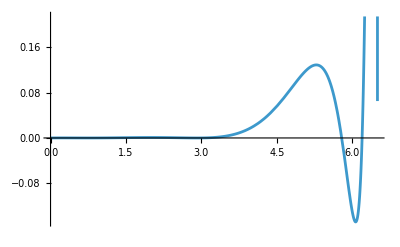

```mathematica
Plot[Det[mat2], {ℰ, 0, vpot}]
```

Here we found the energy levels. Notice that the values of ℰ where the function is cero satisfy the system of equations (mat*[coeff]=0).

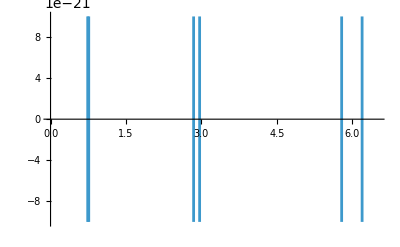

```mathematica
fig= Plot[Det[mat2], {ℰ, 0, vpot}, PlotRange->{-10^-20, 10^-20}]
```

```mathematica
fig[[1]]
```

```mathematica
{{{{},{},{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[2]],Line[{{0.7484764067280265,1.*^-20},{0.7484764067280265,-1.*^-20}}],Line[{{2.9027020518400253,-1.*^-20},{2.9027020518400253,1.*^-20}}],Line[{{5.927016208740115,1.*^-20},{5.927016208740115,-1.*^-20}}]}}},{}}
```

{{{{},{},{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[2]],Line[{{0.748476,1.×10^-20},{0.748476,-1.×10^-20}}],Line[{{2.9027,-1.×10^-20},{2.9027,1.×10^-20}}],Line[{{5.92702,1.×10^-20},{5.92702,-1.×10^-20}}]}}},{}}

```mathematica
aproxroot = fig[[1,1,1,1,3,1]][[2;;-1]]//Map[#[[1,1,1]]&, #]&//Sort
```

{0.739199,0.7595,2.84476,2.96416,5.78811,6.19469}

```mathematica
rval=aproxroot//Map[FindRoot[Det[mat2], {ℰ, #}]&, #]&//Map[ℰ/.#&, #]&
```

{0.739194,0.759528,2.84474,2.96417,5.78909,6.19471}

### Level 1

```mathematica
nval=1;
Do[Subscript[c,i]=., {i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

Unset::norep: Assignment on Subscript for c_1 not found.

Unset::norep: Assignment on Subscript for c_2 not found.

Unset::norep: Assignment on Subscript for c_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

{0.707107,-0.000103738,-0.000420087,0.0000274377,0.0000274377,-0.000103738,0.000420087,0.707107}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

4.8918×10^-7

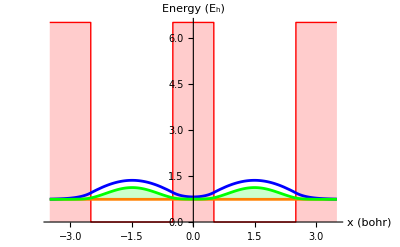

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-lb-la-0.5, la+lb+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

What is the probability of finding one electron within -a-b/2 ≤x≤-b/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-la -lb/2, -lb/2}]
```

0.485302

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

0.0165715

What if φ(x=0)?

```mathematica
1/(√int)φ[x]/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained 1.36258×10^-10 and 4.57464×10^-14 for the integral and error estimates.

1.36258×10^-10

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

2.44961

Upgrade until here, there is are some parts that are missing .

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

Sum::vloc: The variable {i,2}+rval⟦3⟧ cannot be localized so that it can be assigned to numerical values.

∑_({i,2}+rval⟦3⟧) 2 rval⟦i⟧

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

### Level 2

```mathematica
nval=2;
Do[Subscript[c,i]=., {i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707107,0.000123297,0.000415411,-0.0000265255,0.0000265255,-0.000123297,0.000415411,0.707107}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

4.82117×10^-7

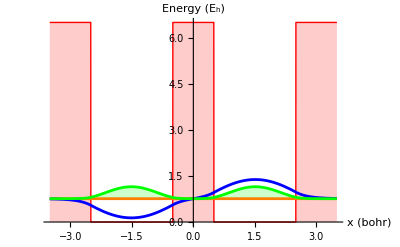

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-lb-la-0.5, la+lb+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

What is the probability of finding one electron within -a-b/2 ≤x≤-b/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-la -lb/2, -lb/2}]
```

0.488373

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

0.00982309

What if φ(x=0)?

```mathematica
1/(√int)φ[x]/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained -1.23584×10^-10 and 4.78079×10^-14 for the integral and error estimates.

-1.23584×10^-10

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

2.50693

Upgrade until here, there is are some parts that are missing .

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

Sum::vloc: The variable {i,2}+rval⟦3⟧ cannot be localized so that it can be assigned to numerical values.

∑_({i,2}+rval⟦3⟧) 2 rval⟦i⟧

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

2 ⟨u_1⟩+2 ⟨u_2⟩+⟨u_3⟩

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩+u_tot

### Level 3

```mathematica
nval=3;
Do[Subscript[c,i]=., {i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.707106,0.000486012,0.00114043,-0.00021351,-0.00021351,0.000486012,-0.00114043,0.707106}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

4.30598×10^-6

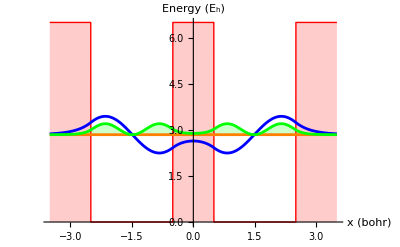

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-lb-la-0.5, la+lb+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

What is the probability of finding one electron within -a-b/2 ≤x≤-b/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-la -lb/2, -lb/2}]
```

0.431418

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

0.0793953

What if φ(x=0)?

```mathematica
1/(√int)φ[x]/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.36722}. NIntegrate obtained -1.85629×10^-12 and 1.40129×10^-16 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

2.73146

Upgrade until here, there is are some parts that are missing .

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

Sum::vloc: The variable {i,2}+rval⟦3⟧ cannot be localized so that it can be assigned to numerical values.

∑_({i,2}+rval⟦3⟧) 2 rval⟦i⟧

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

2 ⟨u_1⟩+2 ⟨u_2⟩+⟨u_3⟩

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩+u_tot

### Level 4

```mathematica
nval=4;
Do[Subscript[c,i]=., {i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.707105,-0.000704019,-0.00116066,0.000240478,-0.000240478,0.000704019,-0.00116066,0.707105}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

4.94077×10^-6

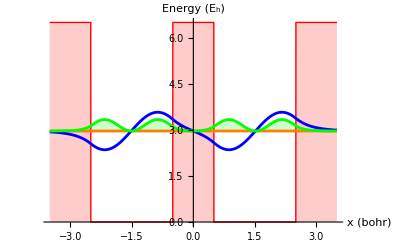

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-lb-la-0.5, la+lb+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

What is the probability of finding one electron within -a-b/2 ≤x≤-b/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-la -lb/2, -lb/2}]
```

0.44844

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

0.0391605

What if φ(x=0)?

```mathematica
1/(√int)φ[x]/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.4999999641296356803699999546324928868801240611219327547587454319}. NIntegrate obtained -2.84255×10^-13 and 1.87165×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

2.87706

Upgrade until here, there is are some parts that are missing .

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

Sum::vloc: The variable {i,2}+rval⟦3⟧ cannot be localized so that it can be assigned to numerical values.

∑_({i,2}+rval⟦3⟧) 2 rval⟦i⟧

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

2 ⟨u_1⟩+2 ⟨u_2⟩+⟨u_3⟩

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩+u_tot

### Level 5

```mathematica
nval=5;
Do[Subscript[c,i]=., {i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{0.705911,-0.0117825,-0.0360802,0.0157672,0.0157672,-0.0117825,0.0360802,0.705911}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

0.00528687

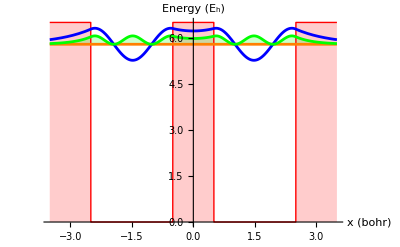

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-lb-la-0.5, la+lb+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

What is the probability of finding one electron within -a-b/2 ≤x≤-b/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-la -lb/2, -lb/2}]
```

0.292228

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

0.212017

What if φ(x=0)?

```mathematica
1/(√int)φ[x]/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.5000000179351824814857839113022984732213743311998205226198868701}. NIntegrate obtained 1.11092×10^-14 and 1.17312×10^-13 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

3.37312

Upgrade until here, there is are some parts that are missing .

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

Sum::vloc: The variable {i,2}+rval⟦3⟧ cannot be localized so that it can be assigned to numerical values.

∑_({i,2}+rval⟦3⟧) 2 rval⟦i⟧

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

2 ⟨u_1⟩+2 ⟨u_2⟩+⟨u_3⟩

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩+u_tot

### Level 6

```mathematica
nval=6;
Do[Subscript[c,i]=., {i,8}];
Evaluate[Table[Subscript[c, i],{i,8}]]=(mat2/.ℰ->rval[[nval]]//NullSpace)[[1]]//Chop
```

{-0.691614,0.0667736,0.0750336,-0.10762,0.10762,-0.0667736,0.0750336,0.691614}

We need to find the normalization constant for φ(x).

```mathematica
int = NIntegrate[
Abs[φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

0.0367803

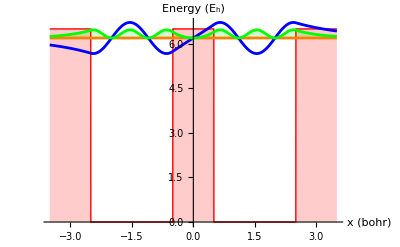

```mathematica
figure[nval]=Plot[{v[x], ℰ,ℰ+(1/(√int)φ[x]), ℰ+(1/(√int)φ[x])^2 }
/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-lb-la-0.5, la+lb+0.5},
PlotRange->All,
AxesLabel->{"x (bohr)", "Energy (E_h)"},
BaseStyle->{FontFamily->"Helvetica", PointSize->14},
PlotStyle->{{Red,Thick},Orange,Blue,Green},
Exclusions->None,
Filling->{1->Axis,4->rval[[nval]]}
]
```

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]
```

1.

What is the probability of finding one electron within -a-b/2 ≤x≤-b/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x,-la -lb/2, -lb/2}]
```

0.299688

What is the probability of finding one electron within x≥a/2

```mathematica
NIntegrate[Abs[1/(√int)φ[x]]^2/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

0.0660754

What if φ(x=0)?

```mathematica
1/(√int)φ[x]/.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -lb/2, lb/2}]
```

Let’s find the uncertainty Δx for one electron in this energy level .

```mathematica
⟨x⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-2.293}. NIntegrate obtained 7.58942×10^-15 and 1.63375×10^-16 for the integral and error estimates.

0

```mathematica
⟨x^2⟩=NIntegrate[Abs[1/(√int)φ[x]]^2 x^2 /.{α->√(2(v0-ℰ)), β->√(2 ℰ)}/.{v0->vpot, a ->la,b->lb, ℰ->rval[[nval]]}//Evaluate, {x, -∞, ∞}]//Chop
```

4.99442

Upgrade until here, there is are some parts that are missing .

Total energy of the system with 5 electrons

```mathematica
Subscript[ℰ, tot]=Sum[2 rval[[i]], {i,2}+rval[[3]]]
```

Sum::vloc: The variable {i,2}+rval⟦3⟧ cannot be localized so that it can be assigned to numerical values.

∑_({i,2}+rval⟦3⟧) 2 rval⟦i⟧

What is the total kinetic energy of the system?

```mathematica
Subscript[k, tot]=Sum[2⟨Subscript[k, i]⟩,{i,2}]+⟨Subscript[k, 3]⟩
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩

What is the total potential energy of the system?

```mathematica
Subscript[U, tot]=Sum[2⟨Subscript[u, i]⟩,{i,2}]+⟨Subscript[u, 3]⟩
```

2 ⟨u_1⟩+2 ⟨u_2⟩+⟨u_3⟩

Notice that k_tot +y U_tot is exactly the total energy of the system:

```mathematica
Subscript[k, tot]+Subscript[u, tot]
```

2 ⟨k_1⟩+2 ⟨k_2⟩+⟨k_3⟩+u_tot

### Summary of the plots

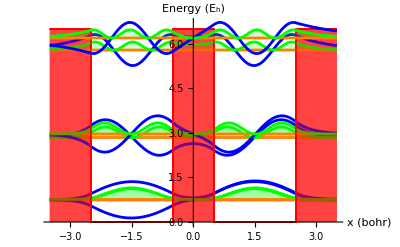

```mathematica
Show@@Table[figure[i],{i,6}]
```

what is the total energy if the system if it has 10 electrons

```mathematica
Subscript[ℰ, tot]=
```

Homo is the higest occupied level, and the lumo is the lower unocupied level.

What is the cohesion Energy  of this system?

energy molecule=energy tot

Energy Atom = 13.2325

Cohesion energy = Emol/2-Eatom

Challenge: What is the case when add another barrier.